## Challenges - 1

BAR CHARTS:

Make a (horizontal) bar chart showing the GDP per capita of all countries in South America. Hints: CountryData[“SouthAmerica”] returns a list of all countries in South America; CountryData[country, “GDPPerCapita”] returns the GDP per capita of a country;

```mathematica
cd1=CountryData["SouthAmerica"]
```

{Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,Falkland Islands,French Guiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
cd2=Map[CountryData[#,"Name"]&, cd1]
```

{Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,Falkland Islands,French Guiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
cd3=Map[CountryData[#, "GDPPerCapita"]&, cd1]
```

{10761.1 $,3345.2 $,7507.16 $,16265.1 $,6104.14 $,5965.13 $,35400. $,8300. $,9998.55 $,6035.14 $,6621.65 $,5259.26 $,17312.6 $,3965.03 $}

```mathematica
cd4=Map[QuantityMagnitude, Map[CountryData[#, "GDPPerCapita"]&, cd2]]
```

{10761.1,3345.2,7507.16,16265.1,6104.14,5965.13,35400.,8300.,9998.55,6035.14,6621.65,5259.26,17312.6,3965.03}

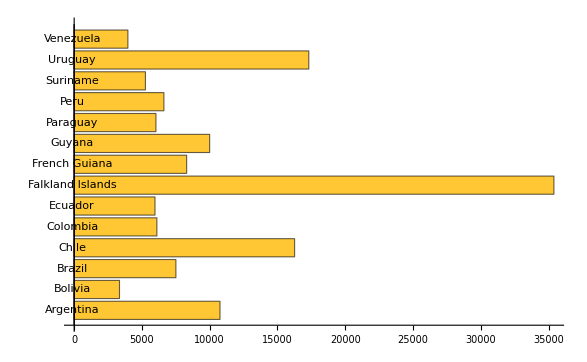

```mathematica
BarChart[cd4,ChartLabels->cd2,BarOrigin->Left]
```

You want to compare male and female life expectancies for different countries. What chart would you make? Create a function that accepts a list of countries as an argument, and makes the appropriate plot. Test it with a list of some countries, maybe the same countries we used as examples in the notebook. Can you draw any conclusion from the plot? Hint: The command CountryData[“Properties”] lists all the quantities that you can get with CountryData.

```mathematica
CountryData["Properties"];
```

```mathematica
lifeExpect[countr_list]:=Module[
{malecd1,femalecd1,countrynamescd1},
malecd1=Map[CountryData[#,"MaleLifeExpectancy"]&,countr];
femalecd1=Map[CountryData[#,"FemaleLifeExpectancy"]&,countr];countrynamescd1=Map[CountryData[#,"Name"]&,countr];
BarChart[Transpose[{malecd1,femalecd1}],ChartLabels->{countrynamescd1,None},ChartLegends->{"Male","Female"},BarOrigin->Left,PlotLabel->"Male/Female Life Expectancy",AxesLabel->{None,"years"}]
]
```

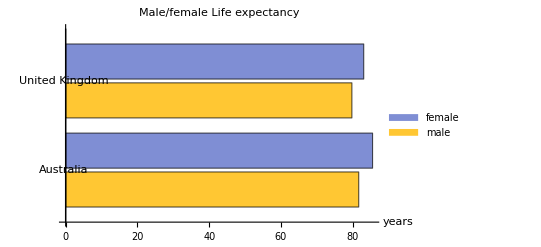

```mathematica
lifeExpect[{"Australia","United Kingdom"}]
```

Create a single-bar stacked bar chart depicting the distribution of the UK population according to city size, dividing cities into four categories: huge (cities with population above one million); large (population above 100,000 but below one million); small (population between 10,000 and 100,000); and tiny (population below 10,000). The bars represent the total number of people in the UK living in huge, large, small and tiny cities. 
Hints: CityData[{All,”UnitedKingdom”}] returns the list of all UK cities in the database. CityData[city,”Population”] returns the population of a given city; the population data may be missing, so you should discard results that match the _Missing pattern. The result will be in the form Quantity[population, People], so you should use the function QuantityMagnitude to get just the population.

```mathematica
cities = CityData[{All,"UnitedKingdom"}];
```

```mathematica
pops = Map[CityData[#, "Population"]&, cities];
```

Define a function that accepts the name of a country as an argument, and returns a list with the total number of people in that country living in huge, large, small and tiny cities. Use this function to generate single-bar stacked bar charts for a few countries, for example France and South Africa.

Using the function you defined above, create a function that accepts a list of countries, and generates a percentile stacked bar chart depicting the fraction of the population living in huge, large, small and tiny cities.

SCATTER PLOTS:

What quantities do you expect will correlate with a country's life expectancy? Inspect the quantities in CountryData["Properties"] and choose a few that you expect to be strongly correlated to life expectancy. Create scatter plots to test your ideas.

Create a function mfDiff that accepts a CountryData’s property (such as “LiteracyFraction” or “GDPPerCapita”) as an argument, and plots a scatter data of that property versus the difference in life expectancies between females and males for all countries. So
mfDiff[“GDPPerCapita”] creates a scatter plot of GDP per capita versus the difference in male/female life expectancies.

Create a function that accepts a year as an argument, and plots a scatter plot of population versus GDP per capita for all countries at that year.

In the first notebook, we defined a function countryPlot that accepts the names of two CountryData properties as arguments, and displays a scatter plot of those properties for all countries in Mathematica’s database. Change this function to make it accept a continent as its third argument. The countries of that continent should be shown as points of a different colour from the other countries.

Modify countryPlot so that when the mouse hovers over it, a tooltip showing the country's name shows up.

Change countryPlot so that the tooltip shows the country’s flag instead of its name.

Modify countryPlot so that when the mouse hovers over it, a tooltip showing a table with relevant information about the country shows up. Information on the table could include the country's name, its capital city, its population, its continent, etc.

Ignore this problem

Create a function that accepts two lists of CountryData’s properties, and creates a grid of scatter plots for every combination of properties.

Create a function that accepts a list of CountryData’s properties, and creates a TabView of scatter plots of literacy versus each of the properties in the list.

LINE PLOTS:

Make a line plot showing the population changes over time for India, China, and the United States. Each point in the plot indicates by how much the population increased compared to the previous year. Hint: look up the definition of the function Differences. Compare with the population plots.

Create a function that accepts a list of countries, and creates a line plot of population over time for those countries, starting in 1920 until the present day.

Modify the function above to plot symbols as well as lines, and associate each symbol with a tooltip that displays the GDP per capita at that time.

Modify the function above to display the percentile population for the given countries, that is, the fraction of the human population in that country.